```mathematica
Input beam visualisation
```

```mathematica
azi={0,1};
rad={1,0};
A=BesselJ[1,r] Exp[-(r/1)^2];
```

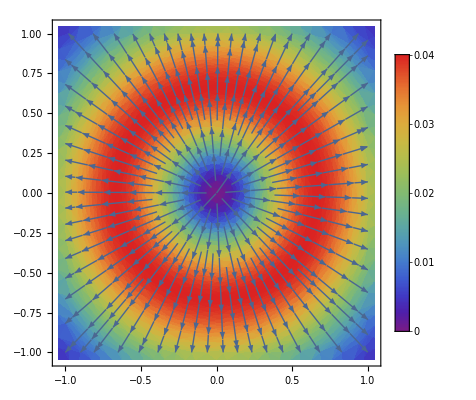

```mathematica
StreamDensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",Abs[A]^2 rad,{r,θ}->{x,y}],{x,-1,1},{y,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

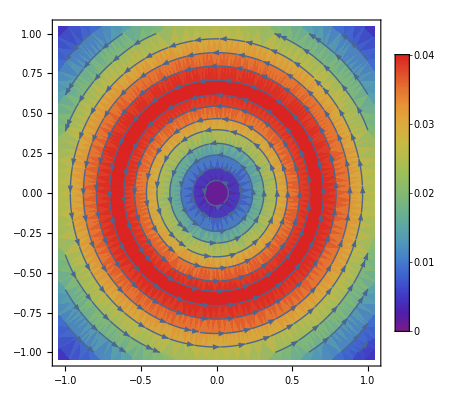

```mathematica
StreamDensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",Abs[A]^2 azi,{r,θ}->{x,y}],{x,-1,1},{y,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

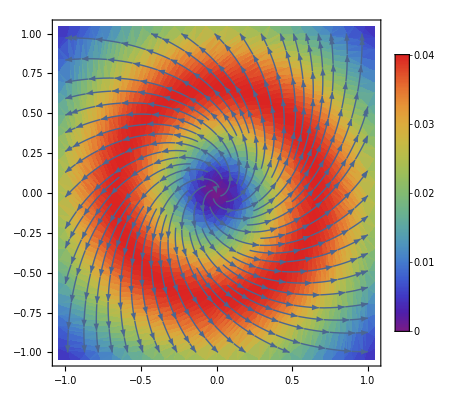

```mathematica
StreamDensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",Abs[A]^2 1/(√2)(azi+rad),{r,θ}->{x,y}],{x,-1,1},{y,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

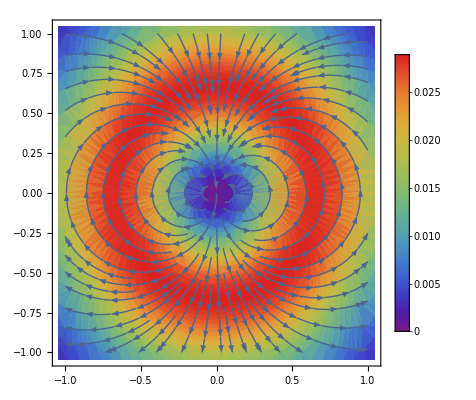

```mathematica
StreamDensityPlot[Evaluate@TransformedField["Polar"->"Cartesian",Abs[A]^2 1/(√2)(Cos[θ] azi-Sin[θ] rad),{r,θ}->{x,y}],{x,-1,1},{y,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

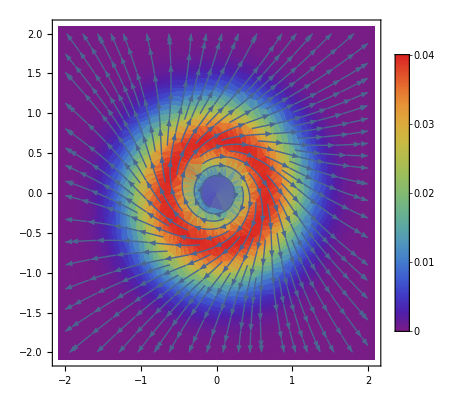

```mathematica
StreamDensityPlot[Evaluate@TransformedField["Polar"->"Cartesian", Abs[A]^2 1/(√(r^2+(1/r^2)))(r rad- (1/r)azi),{r,θ}->{x,y}],{x,-2,2},{y,-2,2},ColorFunction->"Rainbow",PlotLegends->Automatic]
```